```mathematica
(* Copyright 2013 Thomas Trogdon *)
(* This software is distributed under the terms of the GNU General Public License *)
```

```mathematica
AppendTo[$Path,NotebookDirectory[]];
AppendTo[$Path,"~/RHPackage"];
<<RiemannHilbert`;
<<ISTPackage`;
<<ISTPackage`NLS`;
```

## Normal Reflection Coefficient

General::ovfl: Overflow occurred in computation.

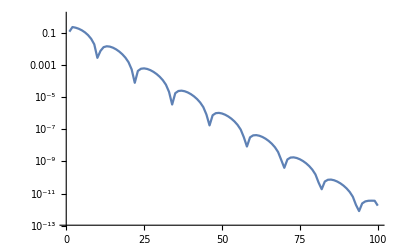
{5.72504×10^-20,-Graphics-}

```mathematica
q[x_]:=Sech[x]/.Underflow[]->0/.Indeterminate->0.;
q[_?InfinityQ]:=0.;
Defocusing[];
LocatePolesNLS[q,40];
H=ScatteringMatrixFiniteNLS[q,100,45];
H[_?InfinityQ]={{1,0},{0,1}};
aa//Clear;bb//Clear;
aa[k_]:=aa[k]=H[k][[1,1]];
bb[k_]:=bb[k]=H[k][[2,1]];
```

```mathematica
ν=Getnu[];
ρ[k_]:=bb[k]/aa[k];
```

```mathematica
SetScatteringData[aa,bb,ρ,LocatePolesNLS[q,40]]
SetParams[.4,.1,10.^(-9),10,20];
h[k_]:=3/(1+Abs[k/2+1/3.2]^8);
Setrsamp[h];
Settimeflag[True];
```

General::ovfl: Overflow occurred in computation.

$Aborted

```mathematica
SetScatteringData[aa,bb,ρ,{},{}]
SetParams[.4,.1,10.^(-9),10,20];
h[k_]:=3/(1+Abs[k/2+1/3.2]^8);
Setrsamp[h];
Settimeflag[True];
```

$Aborted

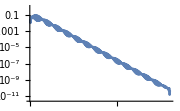

```mathematica
Fun[ρ[#]&,Line[{-9,9}],400]//DCTPlot
```

```mathematica
jump={Fun[{{1-Abs[ρ[#]]^2,-Conjugate[ρ[#]]},{ρ[#],1}}&,Line[{-9,9}],400]};
```

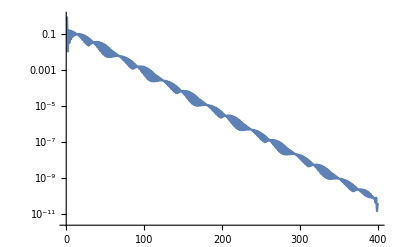

```mathematica
DCTPlot/@jump
```

```mathematica
1-(jump//RHSolve//DomainIntegrate)[[1,2]]/(-Pi)
```

2.41496×10^-12-9.71174×10^-17 ⅈ

## Cauchy Integral Reflection Coefficient

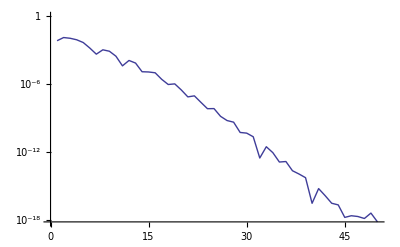
{5.27164×10^-17,-Graphics-}

```mathematica
q[x_]:=.5 /11(x+1)Exp[-x^2]/.Underflow[]->0/.Indeterminate->0.;
q[_?InfinityQ]:=0.
Defocusing[];
LocatePolesNLS[q,40];
H=ScatteringMatrixFiniteNLS[q,50,6];
aa//Clear;bb//Clear;
aa[k_]:=aa[k]=H[k][[1,1]];
bb[k_]:=bb[k]=H[k][[2,1]];

SetParams[.6,.1,10.^(-9),10,20];
h[k_]:=3/(1+Abs[k/2+1/3.2]^8);
Setrsamp[h];
Settimeflag[False];
ν=Getnu[];
ρ[k_]:=bb[k]/aa[k];
```

```mathematica
up=I(ν+.0001);m=50;el=8;
f={Fun[ρ,Line[{-el,0}-up],m],Fun[ρ,Line[{0,el}-up],m],Fun[ρ,Line[{el,0}+up],m],Fun[ρ,Line[{0,-el}+up],m]};
```

```mathematica
mρ//Clear;
mρ[k_]:=mρ[k]=Piecewise[{{Cauchy[f,k], Im[k]< Im[up]}, {ρ[k], True}}];
qNLS//Clear;
qNLS[x_,t_]:=qNLS[x,t]=NLSAuto[x,t];
```

```mathematica
SetScatteringData[aa,bb,mρ,LocatePolesNLS[q,40]]
```

Line[{-3.05,3.05}]

## Plotting: timestring outputs relevant computation times and region information

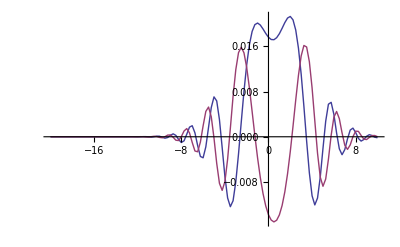

```mathematica
(* Defocusing *)
Monitor[ReImTablePlot[qNLS[x,1.],{x,-20,10,.25},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick],timestring]
```

```mathematica
(* Focusing *)
Monitor[TablePlot[qNLS[x,1.]//Re,{x,-20,10,.25},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick],timestring]
```

$Aborted